# Calculation of Statistical-Mechanical Quantities of Lotka-Volterra Hamiltonian

## (#1): Requisite Data:

## (#1.1): “Standard LV Hamiltonian”

### (#1.1.1): Defining the Hamiltonian:

```mathematica
LVHamiltonian[q_,p_]:=δ Exp[p]-γ p + β Exp[q]-α q;
```

### (#1.1.2): Can we easily exponentiate it without Mathematica freaking out?

```mathematica
Exp[LVHamiltonian[q,p]]
```

ⅇ^(-q α+ⅇ^q β-p γ+ⅇ^p δ)

## (#2): Microcanonical Ensemble Analysis (“Standard Hamiltonian”):

## (#2.1): Obtaining the Area Enclosed by Phase Space Orbits:

### (#2.1.1): Making a plot for visualizing the orbits:

Using the following article for the values of the parameter: https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example

#### (#2.1.1.1): The LV Hamiltonian:

For initial conditions of p = 0.9 and q = 0.9, the constant of the motion under the designation of the four model parameters below is:

```mathematica
LVHamiltonian[0.9,0.9]/.α->2/3/.β->4/3/.γ->1/.δ->1
```

4.23907

#### (#2.1.1.2): The Plot: ([NOTE]: New phase space variables can be negative and positive!)

The space is foliated, but it looks like a strange shape (i.e. not ellipsoidal, obviously). Topologically equivalent to torus, probably.

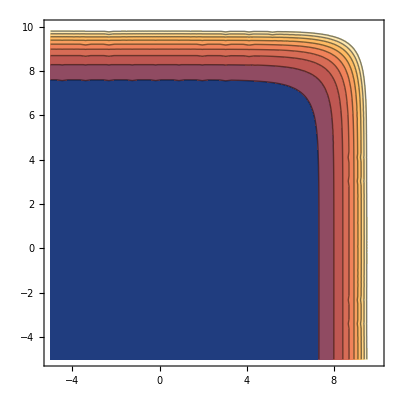

```mathematica
ContourPlot[ⅇ^p+(4 ⅇ^q)/3-p-(2 q)/3,{q,-5,10},{p,-5,10}]
```

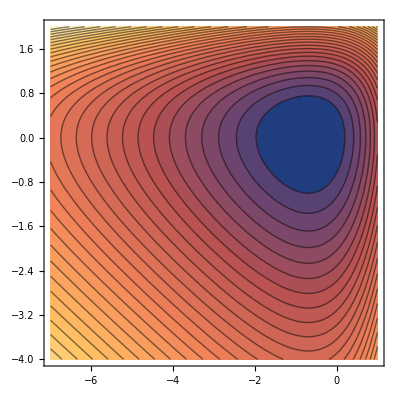

```mathematica
(* α = 2/3, β = 4/3, γ = δ = 1*)
(* These parameters are the ones used in the paper, Figure 1 *)
ContourPlot[1 ⅇ^p-1 p+4/3 Exp[q]-2/3 q,{q,-7,1},{p,-4,2},Contours->30]
```

### (#2.1.2): Trying to Solve for the Bounding Functions:

#### (#2.1.2.1): Seeing how many Solutions are found for the Implicit Equation:

```mathematica
FullSimplify[
Solve[ConstE==LVHamiltonian[q,p],p],
Assumptions-> 
-∞<q<∞&&-∞<p<∞&&
ConstE∈Reals&&α∈Reals&&β∈Reals&&δ∈Reals&&γ∈Reals]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→-(ConstE+q α-ⅇ^q β+γ ProductLog[-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ}}

Only one solution is found... That is likely because, although we specified that α, β, γ, and δ are positive, we did not specify their relative differences.

```mathematica
LVHamiltonian[q,p]/.p->-(ConstE+q α-ⅇ^q β+γ ProductLog[0,-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ//Simplify
```

ConstE

```mathematica
LVHamiltonian[q,p]/.p->-(ConstE+q α-ⅇ^q β+γ ProductLog[1,-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ//Simplify
```

ConstE

Wow! It actually works. Nice!

#### (#2.1.2.2): Manually Entering the Solutions We Got:

```mathematica
pPlus=(-ConstE+β Exp[q]-α q)/γ-ProductLog[0,δ/γ Exp[(-ConstE+β Exp[q]-α q)/γ]];
pMinus=(-ConstE+β Exp[q]-α q)/γ-ProductLog[1,δ/γ Exp[(-ConstE+β Exp[q]-α q)/γ]];
```

#### (#2.1.2.3): Since the first integral is just over 1, the integrand for the next integral is just p^+-p^-. So, what is that?

```mathematica
FullSimplify[
pPlus-pMinus,
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals&&δ∈Reals
]
```

-ProductLog[(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]

#### (#2.1.2.4): Test Run Using a Dummy Integrand, ∫dx (-W_0(x)+W_1(x)):

Below, x stands for the insane thing in the ProductLog[].

```mathematica
FullSimplify[
Integrate[
-ProductLog[0,x]+ProductLog[1,x],
{x, a, b}],
Assumptions->a>0&&b>0&&b>a]
```

ⅇ^ProductLog[a]-ⅇ^ProductLog[b]-ⅇ^ProductLog[1,a]+ⅇ^ProductLog[1,b]+a ProductLog[a]-b ProductLog[b]-a ProductLog[1,a]+b ProductLog[1,b]

#### (#2.1.2.5): Trying the Whole Thing:

```mathematica
Integrate[
-ProductLog[0,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ],
{q, -5,5},
Assumptions->
ConstE∈Reals&&
α∈Reals&&β∈Reals&&δ∈Reals&&γ∈Reals
]
```

Integrate[-ProductLog[(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ],{q,-5,5},Assumptions→ConstE∈ℝ&&α∈ℝ&&β∈ℝ&&δ∈ℝ&&γ∈ℝ]

#### (#2.1.2.6): Can we get something closed-form of (∫_a)^b dxW^(e^(-h x))?

It seems like we can:

```mathematica
Integrate[
ProductLog[0,Exp[-h x]],{x, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

((ProductLog[ⅇ^(-a h)]-ProductLog[ⅇ^(-b h)]) (2+ProductLog[ⅇ^(-a h)]+ProductLog[ⅇ^(-b h)]))/(2 h)

#### (#2.1.2.7): How about the indefinite form of this: ∫dxW^(e^(-h x))?

I also managed to derive this. Yay!

```mathematica
Integrate[
ProductLog[0,Exp[a x]],x,
Assumptions->a∈Reals]
```

ProductLog[ⅇ^(a x)]/a+(ProductLog[ⅇ^(a x)]^2)/(2 a)

#### (#2.1.2.8): Can we get something closed-form of ∫dxW^(e^(e^x))?

Here, we cannot get it.

```mathematica
Integrate[
ProductLog[Exp[Exp[x]+x]],{x, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[ProductLog[ⅇ^(ⅇ^x+x)],{x,a,b},Assumptions→a>0&&b>0&&b>a]

#### (#2.1.2.9): After some u-substitution, I think we can get ∫dxW^(e^(e^x))into something like this:

And this has at least some kind of crazy solution:

```mathematica
Integrate[
Log[ProductLog[x]]/ProductLog[x],{x, a, b},
Assumptions->a>0&&b>0&&b>a]
```

$Aborted

#### (#2.1.2.10): After a u-substitution on ∫dx W(a^(e^(e^bx+cx))), I found this integral:

It still can’t get it, but it must be possible...

```mathematica
Integrate[
Exp[u]ProductLog[0,u],{u, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[ⅇ^u ProductLog[u],{u,a,b},Assumptions→a>0&&b>0&&b>a]

```mathematica
Integrate[
v^2 Exp[Exp[v]+v],{v, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[ⅇ^(ⅇ^v+v) v^2,{v,a,b},Assumptions→a>0&&b>0&&b>a]

```mathematica
Integrate[
v^v Log[V],{v, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[v^v Log[V],{v,a,b},Assumptions→a>0&&b>0&&b>a]

```mathematica
Integrate[
Log[u]ProductLog[A Exp[u]],{u, a, b},
Assumptions->
A>0&&a>0&&b>0&&b>a]
```

Integrate[Log[u] ProductLog[A ⅇ^u],{u,a,b},Assumptions→A>0&&a>0&&b>0&&b>a]

## (#2.2): Suppose it’s an “ecological ideal gas,” where no q is featured in H:

We pretend that, just for computation’s sake, that there is no q in the Hamiltonian, or rather that q only ranges from 0 to some fixed “box” size of length L.

### (#2.2.1): Solving for the maximum value p can take with a fixed E:

```mathematica
Solve[ConstE==δ Exp[p]-γ p ,p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→(-ConstE-γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/γ}}

#### (#2.2.1.1): Verifying the upper bound is correct:

```mathematica
δ Exp[p]-γ p /.p->(-ConstE-γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/γ//Simplify
```

ConstE

#### (#2.2.1.2): Verifying the lower bound is correct:

```mathematica
δ Exp[p]-γ p /.p->(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ//Simplify
```

ConstE

#### (#2.2.1.3): What happens when E is quite small? Does it go back to something like √(2mE)?

```mathematica
Series[(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ,{ConstE,0,5}]//FullSimplify
```

-ProductLog[1,-δ/γ]-ConstE/(γ+γ ProductLog[1,-δ/γ])-(ProductLog[1,-δ/γ] ConstE^2)/(2 (γ^2 (1+ProductLog[1,-δ/γ])^3))+((ProductLog[1,-δ/γ]-2 ProductLog[1,-δ/γ]^2) ConstE^3)/(6 γ^3 (1+ProductLog[1,-δ/γ])^5)-((ProductLog[1,-δ/γ] (1-8 ProductLog[1,-δ/γ]+6 ProductLog[1,-δ/γ]^2)) ConstE^4)/(24 (γ^4 (1+ProductLog[1,-δ/γ])^7))+((ProductLog[1,-δ/γ]-22 ProductLog[1,-δ/γ]^2+58 ProductLog[1,-δ/γ]^3-24 ProductLog[1,-δ/γ]^4) ConstE^5)/(120 γ^5 (1+ProductLog[1,-δ/γ])^9)+O[ConstE]^6

#### (#2.2.1.4): Want to see the contours:

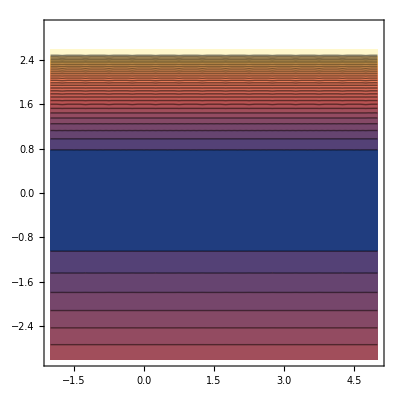

```mathematica
ContourPlot[1 ⅇ^p-1 p,{q,-2,5},{p,-3,3},Contours->30]
```

#### (#2.2.1.5): How about the contours with very small q?

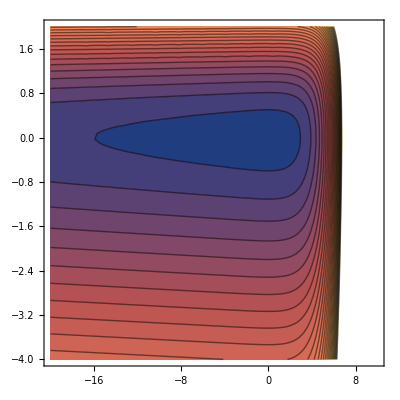

```mathematica
ContourPlot[1 ⅇ^p-1 p+0.01Exp[q]-0.01q,{q,-20,10},{p,-4,2},Contours->30]
```

#### (#2.2.1.6): Same thing except for small p:

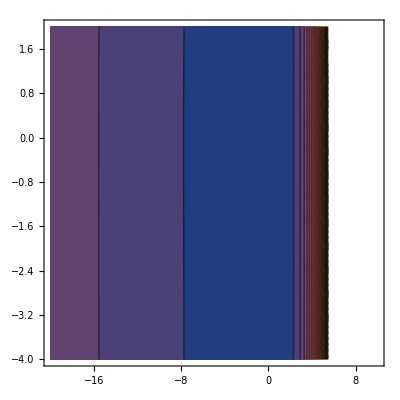

```mathematica
ContourPlot[0.01 ⅇ^p-0.01p+1Exp[q]-1 q,{q,-20,10},{p,-4,2},Contours->30]
```

## (#3): Canonical Ensemble Analysis:

## (#3.1): Partition Function:

### (#3.1.1): Defining the entire Partition Function:

```mathematica
LVZ[θ_]:=Exp[-θ LVHamiltonian[q,p]]
```

### (#3.1.2): Defining the Z_p Part:

```mathematica
LVZp[θ_]:=Exp[-θ(δ Exp[p]-γ p)]
```

### (#3.1.3): Defining the Z_q Part:

```mathematica
LVZq[θ_]:=Exp[-θ(β Exp[q]-α q)]
```

### (#3.1.4): Integrating the Z_p Part:

```mathematica
LVZpIntegral=Integrate[LVZp[θ],{p,-∞,∞},Assumptions->θ∈Reals&&δ∈Reals&&γ ∈Reals]
```

ConditionalExpression[(δ θ)^(-γ θ) Gamma[γ θ], (γ>0&&δ>0&&θ>0)||(γ<0&&δ<0&&θ<0)]

### (#3.1.5): Integrating the Z_q Part:

```mathematica
LVZqIntegral=Integrate[LVZq[θ],{q,-∞,∞},Assumptions->θ∈Reals&&α∈Reals&&β ∈Reals]
```

ConditionalExpression[(β θ)^(-α θ) Gamma[α θ], (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

### (#3.1.6): Cross-checking: Z_p Z_q should equal Z:

```mathematica
LVZIntegral=Integrate[LVZ[θ],{q,-∞,∞},{p,-∞,∞},Assumptions->θ∈Reals&&α∈Reals&&β ∈Reals&&δ∈Reals&&γ ∈Reals]
```

ConditionalExpression[(β θ)^(-α θ) (δ θ)^(-γ θ) Gamma[α θ] Gamma[γ θ], (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

We need to confirm that the result is the same as doing the single integral all at once.

```mathematica
LVZpIntegral LVZqIntegral - LVZIntegral
```

ConditionalExpression[0, ]

### (#3.1.7): Plotting Z(θ) with some test parameters:

According to the [following link on the Wiki page about the LV equations](https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example), there are closed cycles for α = 2/3, β = 4/3, γ = 1, and δ = 1. So, let’s use those values while checking these plots.

#### (#3.1.7.1): Plotting Z(θ) with test parameters:

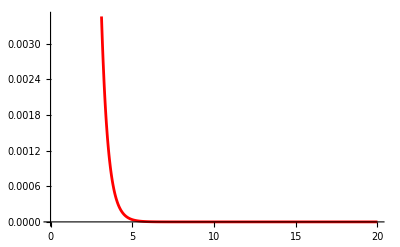

```mathematica
Plot[
LVZIntegral/.α->2/3/.β->4/3/.γ->1/.δ->1,
{θ,0,20},
PlotStyle->Red
]
```

#### (#3.1.7.2): Plotting Z(T) — remember that θ = 1/(k_B T)—with test parameters:

General::munfl: 1/99.7982^166.33 is too small to represent as a normalized machine number; precision may be lost.

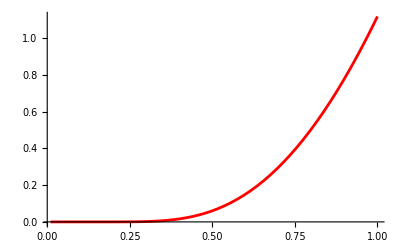

```mathematica
Plot[
LVZIntegral/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T,
{T,0.01,1.00},
PlotStyle->Red
]
```

## (#3.2): Average Energy, ⟨E⟩=-∂/(∂ β)log(Z):

### (#3.2.1): Quantitative calculation using the standard formula:

```mathematica
LVEnergyAverage=-D[Log[LVZIntegral],θ]//FullSimplify
```

ConditionalExpression[α+γ+α Log[β θ]+γ Log[δ θ]-α PolyGamma[0,α θ]-γ PolyGamma[0,γ θ], (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

Just need to check if I can simplify this with another form:

```mathematica
(α(1+Log[β θ]-PolyGamma[0,α θ])+γ(1+Log[δ θ]-PolyGamma[0,γ θ]) )-LVEnergyAverage//FullSimplify
```

ConditionalExpression[0, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

### (#3.2.2): Plotting ⟨E⟩(θ ) with some test parameters:

#### (#3.2.2.1): Plotting ⟨E⟩(θ) with test parameters:

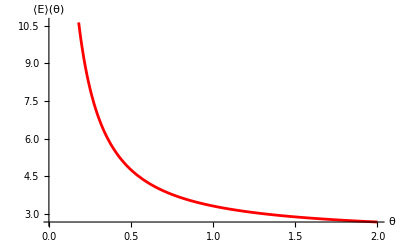

```mathematica
Plot[
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1,
{θ,0.01,2},
PlotStyle->Red,
AxesLabel->{"θ","⟨E⟩(θ)"}
]
```

#### (#3.3.2.2): Plotting ⟨E⟩(T) — remember that θ = 1/(k_B T)—with test parameters:

[NOTE]: It appears there is no minimum average energy.

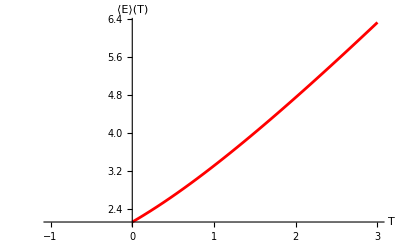

```mathematica
Plot[
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T,
{T,-1,3},
PlotStyle->Red,
AxesLabel->{"T","⟨E⟩(T)"}
]
```

At zero temperature, the average energy is not zero. So, can we find the value of the thing at T = 0?

```mathematica
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T
```

ConditionalExpression[5/3+Log[1/T]+2/3 Log[4/(3 T)]-2/3 PolyGamma[0,2/(3 T)]-PolyGamma[0,1/T], T>0]

```mathematica
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T/.T->0.000000000000000000000000000001
```

2.12876

```mathematica
Limit[LVEnergyAverage/.θ->1/T,T->0]
```

ConditionalExpression[Undefined, (α≥0||β≥0)&&(α≤0||β≤0)]

```mathematica
Series[LVEnergyAverage/.θ->1/T,{T,0,5}]
```

ConditionalExpression[Piecewise[{{(α+γ-α Log[α/T]+α Log[β/T]-γ Log[γ/T]+γ Log[δ/T])+T+((α+γ) T^2)/(12 α γ)+((-α^3-γ^3) T^4)/(120 α^3 γ^3)+O[T]^6, 0≤Arg[γ/T]<π||!Series[Arg[γ/T]≥π,{T,0,6}]}, {π γ Cot[(π γ)/T+O[T]^6] Floor[Arg[γ/T]/π]+(ⅈ (-ⅈ α-ⅈ γ+π γ+ⅈ α Log[α/T]-ⅈ α Log[β/T]+ⅈ γ Log[γ/T]-ⅈ γ Log[δ/T])+T+((α+γ) T^2)/(12 α γ)+((-α^3-γ^3) T^4)/(120 α^3 γ^3)+O[T]^6), True}}], ]

## (#3.3): Variance of Average Energy, ⟨(ΔE)^2⟩=-(∂⟨E⟩)/(∂β)=(∂^2 ln(Z))/(∂β^2):

### (#3.3.1): Quantitative calculation using the standard formula:

```mathematica
LVEnergyVariance=-D[LVEnergyAverage,θ]//FullSimplify
```

ConditionalExpression[-(α+γ-α^2 θ PolyGamma[1,α θ]-γ^2 θ PolyGamma[1,γ θ])/θ, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

Check the above against the other formula:

```mathematica
LVEnergyVariance-D[Log[LVZIntegral],{θ,2}]//FullSimplify
```

ConditionalExpression[0, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

Is there really no dependence on β or δ?

```mathematica
D[Log[LVZIntegral],{θ,2}]//FullSimplify
```

ConditionalExpression[-(α+γ-α^2 θ PolyGamma[1,α θ]-γ^2 θ PolyGamma[1,γ θ])/θ, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

One more check: rewriting the equations above algebraically:

### (#3.3.2): Plotting ⟨(ΔE)^2⟩(θ) with some test parameters:

#### (#3.3.2.1): Plotting ⟨(ΔE)^2⟩(θ) with test parameters:

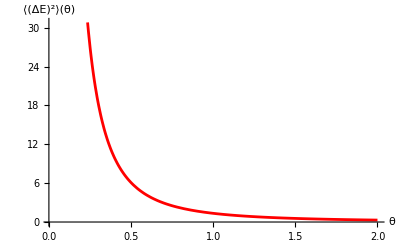

```mathematica
Plot[
LVEnergyVariance/.α->2/3/.β->4/3/.γ->1/.δ->1,
{θ,0.01,2},
PlotStyle->Red,
AxesLabel->{"θ","⟨(ΔE)^2⟩(θ)"}
]
```

#### (#3.2.2.2): Plotting ⟨(ΔE)^2⟩(T) — remember that θ = 1/(k_B T)—with test parameters:

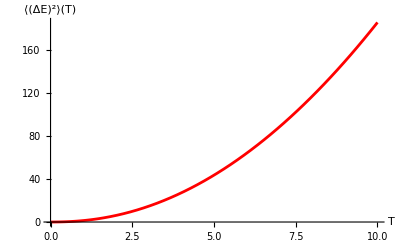

```mathematica
Plot[
LVEnergyVariance/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T,
{T,0,10},
PlotStyle->Red,
AxesLabel->{"T","⟨(ΔE)^2⟩(T)"}
]
```

## (#3.4): “Heat” Capacity, C_v=⟨(ΔE)^2⟩/(k_B T^2):

### (#3.4.1): Quantitative calculation using the standard formula:

```mathematica
LVHeatCapacity=θ^2 LVEnergyVariance//FullSimplify
```

ConditionalExpression[-θ (α+γ-α^2 θ PolyGamma[1,α θ]-γ^2 θ PolyGamma[1,γ θ]), (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

```mathematica
LVHeatCapacity/.θ->1/(kB T)
```

ConditionalExpression[-(α+γ-(α^2 PolyGamma[1,α/(kB T)])/(kB T)-(γ^2 PolyGamma[1,γ/(kB T)])/(kB T))/(kB T), ]

### (#3.4.2): Plotting C_v(θ) with some test parameters:

#### (#3.4.2.1): Plotting C_v(θ) with test parameters:

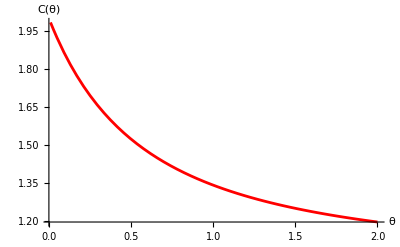

```mathematica
Plot[
LVHeatCapacity/.α->2/3/.β->4/3/.γ->1/.δ->1/.T->1/θ,
{θ,0.01,2},
PlotStyle->Red,
AxesLabel->{"θ","C(θ)"}
]
```

#### (#3.4.2.2): Plotting C_v(T) — remember that θ = 1/(k_B T)—with test parameters:

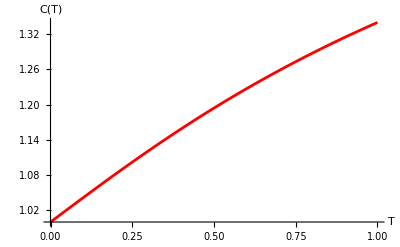

```mathematica
Plot[
LVHeatCapacity/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T,
{T,0.0001,1},
PlotStyle->Red,
AxesLabel->{"T","C(T)"}
]
```

Wow. It appears to asymptote to 2. I did not expect that.

## (#3.5): Entropy, S=-k_B θ^2∂/(∂θ)(ln(Z))/θ:

### (#3.5.1): Quantitative calculation using the standard formula:

```mathematica
LVEntropy=-θ^2 D[ Log[LVZIntegral]/θ,{θ}]//FullSimplify
```

ConditionalExpression[θ (α+γ+γ Log[δ θ])+Log[(δ θ)^(-γ θ) Gamma[α θ] Gamma[γ θ]]-θ (α PolyGamma[0,α θ]+γ PolyGamma[0,γ θ]), (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

Checking against algebraic rewriting:

```mathematica
(θ(α+γ+γ Log[δ θ]-α PolyGamma[0,α θ]-γ PolyGamma[0,γ θ])+Log[(δ θ)^(-γ θ) Gamma[α θ] Gamma[γ θ]])-LVEntropy//FullSimplify
```

ConditionalExpression[0, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

Check against another formula: S = ⟨E⟩/T+ k_B ln(Z) or S=k_B(β ⟨E⟩ + ln(Z))

```mathematica
LVEntropy-(θ LVEnergyAverage+ Log[LVZIntegral])//FullSimplify
```

ConditionalExpression[0, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

In terms of temperature:

```mathematica
LVEntropy/.θ->1/T//FullSimplify
```

ConditionalExpression[(α+γ+γ Log[δ/T]+T Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T])/T, (T>0&&α>0&&β>0)||(T<0&&α<0&&β<0)]

Yeah. It doesn’t do much...

### (#3.5.2): Plotting S(θ) with some test parameters:

#### (#3.5.2.1): Plotting S(θ) with test parameters:

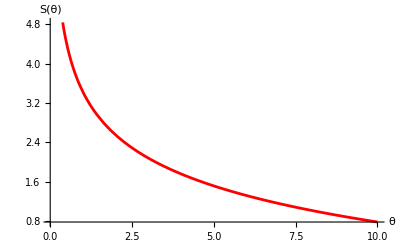

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1,
{θ,0.01,10},
PlotStyle->Red,
AxesLabel->{"θ","S(θ)"}
]
```

#### (#3.5.2.2): Plotting S(T) — remember that θ = 1/(k_B T)—with test parameters:

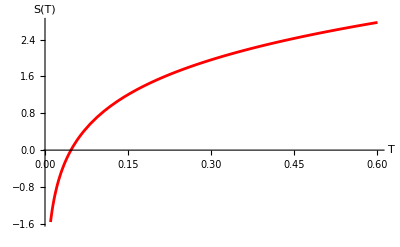

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T,
{T,0.01,0.6},
PlotStyle->Red,
AxesLabel->{"T","S(T)"}
]
```

## (#3.6): Free Energy, F=-k_BT log(Z):

### (#3.6.1): Quantitative calculation using the standard formula:

```mathematica
LVFreeEnergy=-1/θ Log[LVZIntegral]//FullSimplify
```

ConditionalExpression[-Log[(β θ)^(-α θ) (δ θ)^(-γ θ) Gamma[α θ] Gamma[γ θ]]/θ, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]

### (#3.6.2): Plotting F(θ) with some test parameters:

#### (#3.6.2.1): Plotting F(θ) with test parameters:

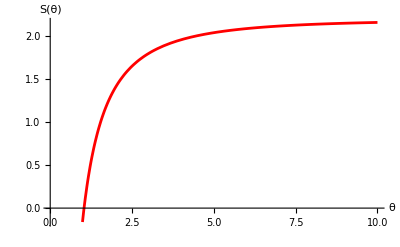

```mathematica
Plot[
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1,
{θ,0.01,10},
PlotStyle->Red,
AxesLabel->{"θ","S(θ)"}
]
```

#### (#3.6.2.2): Plotting F(T) — remember that θ = 1/(k_B T)—with test parameters:

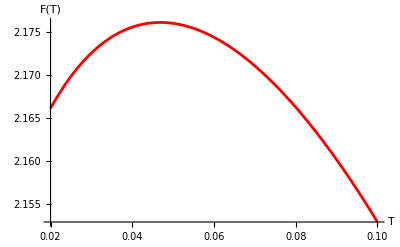

```mathematica
Plot[
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1/.θ->1/T,
{T,0.02,0.1},
PlotStyle->Red,
AxesLabel->{"T","F(T)"}
]
```

## (#3.X): Information Geometry:

#### (#3.X.Y): Fischer Information Metric:

The metric is one-dimensional because there is only one Lagrange multiplier in the Partition Function above.

```mathematica
FischerMetric11LV=D[-Log[LVZIntegral],{θ, 2}]//FullSimplify
```

ConditionalExpression[(α+γ-θ (α^2 PolyGamma[1,α θ]+γ^2 PolyGamma[1,γ θ]))/θ, (α>0&&β>0&&θ>0)||(α<0&&β<0&&θ<0)]